# Evaluation

BX Pan
2017.9.18

There was some variability depending on the geo-graphical area. For instance, over Europe, the anomaly correlations decreased much quicker than over the Northern Hemisphere extratropics as a whole.

Miyakoda et al. (1986) used a 10-day running mean for both the forecasts and the observed data in an attempt to obtain positive skills by filtering out the unpredictable components, most especially the baroclinic eddies

“They were in effect arguing about artifacts induced by sampling at too low a resolution.”

## Cutting

```mathematica
S2SCut[polygon_,s2sdirectory_]:=Block[
{cpcprecip,cpclat,cpclon,cpctime,s2sprecip,s2slat,s2slon,s2stime,
 year=StringTake[StringCases[s2sdirectory,"_"~~__~~"-"],{2,5}][[1]],
 interval,
 points,indexes,cpcdirectory},
    cpcdirectory={"/Users/lambda/Documents/Data/CPC_Precipitation/global/precip."<>year<>".nc",   
            "/Users/lambda/Documents/Data/CPC_Precipitation/global/precip."<>ToString[ToExpression[year]+1]<>".nc"};
	{cpcprecip,cpclat,cpclon,cpctime}=Block[{test1,test2},
		test1=Map[Import[cpcdirectory[[1]],{"Datasets",#}]&,{"precip","lat","lon","time"}];
		test2=Map[Import[cpcdirectory[[2]],{"Datasets",#}]&,{"precip","lat","lon","time"}];
		Table[Join[test1[[i]],test2[[i]]],{i,4}]];
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[s2sdirectory,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
	interval=Map[Position[Abs[cpctime-#[s2stime]],Min[Abs[cpctime-#[s2stime]]]][[1,1]]&,{Min,Max}];	
    cpcprecip=Block[{DownScale,size},
        DownScale[data_,ratio_]:=Block[{convoluter},
			(* This Function performs spacial average downscaling of 2D data through uniform convolution ratio is kind like {5,4}*) 
			convoluter = Block[{net},
   			net = NetInitialize[ConvolutionLayer[1, ratio, "Stride" -> ratio, 
   						"Input" -> Flatten[{1, Dimensions[data]}]]];
               NetReplacePart[net, {"Weights" -> ConstantArray[1./(ratio/.List->Times), Flatten[{1, 1, ratio}]]}]];
            (convoluter@{data})[[1]]];
        size={Round[Abs[s2slat[[2]]-s2slat[[1]]]/Abs[cpclat[[2]]-cpclat[[1]]]],
          Round[Abs[s2slon[[2]]-s2slon[[1]]]/Abs[cpclon[[2]]-cpclon[[1]]]]};
        Map[DownScale[#,size]&,cpcprecip[[interval[[1]];;interval[[2]]]]]];
    points=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,points]];
    cpcprecip=Map[cpcprecip[[;;,#[[1]],#[[2]]]]&,indexes];
    s2sprecip=Block[{scale,offset,origin},
        {scale,offset}=Import[s2sdirectory,"Annotations"][[6,1;;2,2]];
        origin=Map[(s2sprecip[[;;,;;,#[[1]],#[[2]]]]*scale+offset)&,indexes];
        Transpose[Table[If[i==1,origin[[;;,1,;;]],origin[[;;,i,;;]]-origin[[;;,i-1,;;]]],{i,Dimensions[origin][[2]]}]]];
    {cpcprecip,s2sprecip}]
```

#### Example

```mathematica
polygon=westconus[[1]];
s2sdirectory="/Users/lambda/Documents/Data/S2S/BoM/Bom_1981-01-01.nc";
```

```mathematica
{cpcprecip,s2sprecip}=S2SCut[polygon,s2sdirectory];
```

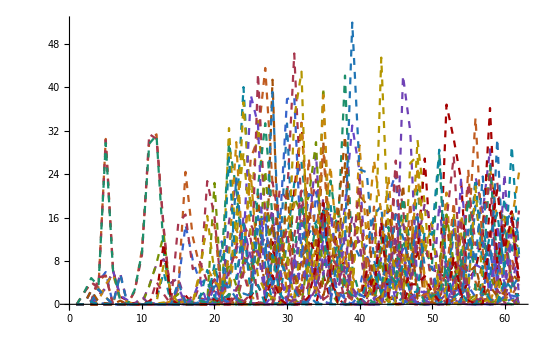
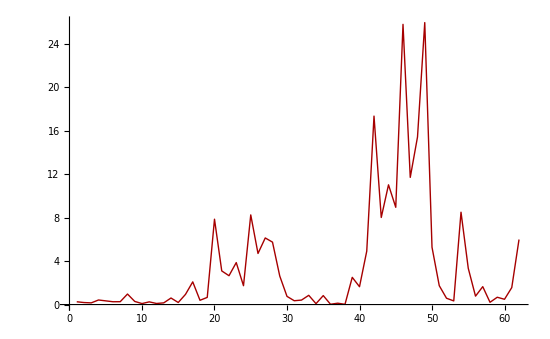

```mathematica
grid=2;
{ListLinePlot[Table[s2sprecip[[grid,;;,i]],{i,Dimensions[s2sprecip][[3]]}],
	PlotStyle->Dashed,
	PlotRange->Full,ImageSize->550],
 ListLinePlot[cpcprecip[[grid,;;]],
    PlotStyle->Thick,PlotRange->Full,ImageSize->550]}
```

## Evaluation

Deterministic Scores

Time Scale

Daily

Weekly

Spatial Scale

Grid

Area Average

Correlation Coefficient(r^2) and Root Mean Square Error(RMSE) are probably not the most suitable for assessing probabilistic forecasts after 10 days, but they are the most widely used for evaluating medium-range weather forecasting and they were used in previous papers on monthly forecasting. It should be Beat Climatology and Persistence (Molteni et al., 1986).

Example: BoM Dataset

#### Sample Collection

The Oct to Feb hindcasts for the West Coast CONUS were gathered as follows. Together there are 161 boreal winter months(33 years).

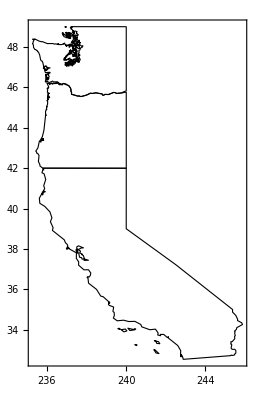

```mathematica
westconus=Block[{ow,ca},
	ow=Import["/Users/lambda/Documents/Data/GeoDivision/West Coast CONUS/oregonwashington.mx"];
	ca=Import["/Users/lambda/Documents/Data/GeoDivision/West Coast CONUS/california.mx"];
	Polygon[Flatten[{ow[[1]],ca[[1]]},1]]];
polygon=westconus[[1]];
(*polygon in the form of {subpoly1,subpoly2,...},subpoly in th form of {{long1,lat1},{long2,lat2}...}*)
Graphics[{EdgeForm[Black],FaceForm[None],westconus},Frame->True]
```

```mathematica
CollectSamples[dataname_,polygon_]:=Block[{dataset,data},
	dataset=Block[{},
		SetDirectory["/Users/lambda/Documents/Data/S2S/"<>dataname];
		Map["/Users/lambda/Documents/Data/S2S/"<>dataname<>"/"<>#&,
			Flatten[Table[FileNames["*-"<>month<>"-*.nc"],{month,{"01","02","10","11","12"}}]]]];
    data=Block[{origin=Map[S2SCut[polygon,#]&,dataset],position},
		position=Position[origin, _?(# <-1.0 &)];
		Map[If[Length[#]==4,Set[origin[[#[[1]],#[[2]],#[[3]],#[[4]]]],0.0],
		    If[Length[#]==5,Set[origin[[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]],0.0],
			If[Length[#]==3,Set[origin[[#[[1]],#[[2]],#[[3]]]],0.0]]]]&,position];
		origin];
	Export["/Users/lambda/Documents/Data/S2S/"<>dataname<>"/"<>dataname<>"_WestCONUS.mx",data];
	data];
```

```mathematica
SetDirectory["/Users/lambda/Documents/Data/S2S/"];
datanames=FileNames[][[{1,2,4,5,6,7,8,9,10,11,12}]];
TableForm[Map[Block[{tempt=Import["/Users/lambda/Documents/Data/S2S/"<>#<>"/"<>#<>"_WestCONUS.mx"]},
	Flatten[{#,Dimensions[tempt[[;;,2]]]}]]&,datanames],
	TableHeadings->{None, {"Name","Months","Grids","Length","EnsembleSize"}},
	TableAlignments->Center]
```

Name | Months | Grids | Length | EnsembleSize
BoM | 161 | 13 | 62 | 32
CMA | 105 | 33 | 60 | 3
ECCC | 100 | 33 | 32 | 3
ECMWF | 97 | 33 | 46 | 10
HCMR | 130 | 33 | 62 | 9
ISACCNR | 150 | 33 | 31 | 1
JMA | 150 | 33 | 34 | 4
KMA | 80 | 33 | 60 | 2
MeteoFrance | 105 | 33 | 61 | 14
NCEP | 60 | 33 | 44 | 3
UKMO | 115 | 33 | 60 | 2

#### ReArrange

```mathematica
data=Block[{name="ECMWF"},
	Import["/Users/lambda/Documents/Data/S2S/"<>name<>"/"<>name<>"_WestCONUS.mx"]];
```

```mathematica
SkillSequence[data_,score_]:=Block[{observation,simulation,size,grids,length,tempt,ensemble,Pmean,Pensemble},
	{size,tempt,grids,length}=Dimensions[data];
	ensemble=Dimensions[data[[1,2]]][[-1]];
	Pensemble=Table[Table[Table[score[data[[;;,1,grid,day]],data[[;;,2,grid,day,member]]],{day,length}],
		{grid,grids}],{member,ensemble}];
	Pmean=Table[Table[score[data[[;;,1,grid,day]],Map[Mean,data[[;;,2,grid,day]]]],{day,length}],{grid,grids}];
	{Pensemble,Pmean}];
```

```mathematica
RMSE[simu_,obser_]:=Sqrt[Mean[(simu-obser)^2.]];
score=Correlation;
{Pensemble,Pmean}=SkillSequence[data,score];
```

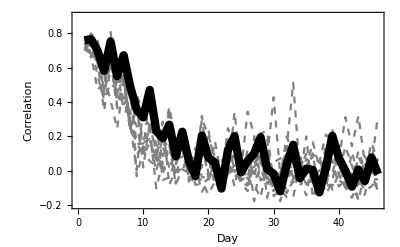

```mathematica
grid=15;
Show[{ListLinePlot[Pensemble[[;;,grid,;;]],PlotRange->{-0.2,0.9},PlotStyle->Table[{Gray,Dashed},Length[Pensemble]]],
ListLinePlot[Pmean[[grid,;;]],PlotStyle->{Thickness->0.015,Black}]},
Frame->True,
BaseStyle->20,
FrameLabel->{"Day",ToString[score]}]
```

Probabilistic Scores

#### Relative Operating Characteristics (ROC) Scores

The relative operating characteristics (ROC) scores are based on contingency tables giving the number of observed occurrences and nonoccurrences of an event as a function of the forecast occurrences and nonoccurrences of that event. The events are defined as binary, for instance, the probability that 2-m temperature is in the upper tercile. (Stanski et al. 1989; Mason and Graham 1999; Kharin and Zwiers 2003)

#### Brier Skill Scores

#### Continuous Ranked Probability Skill Score

#### Reliability diagrams

#### Rank Histograms

#### Kullback-Leibler divergence

## History of Attempts

```mathematica
Tuples[{1, 2}, 2]
```

{{1,1},{1,2},{2,1},{2,2}}

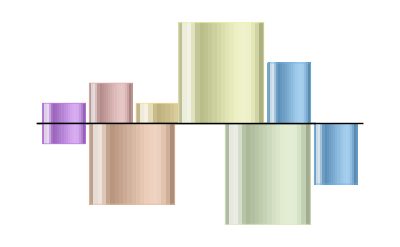

```mathematica
Rotate[Show[{RectangleChart[{{1,1},{1,2},{2,1},{2,-5},{1,-3}},
ChartElementFunction -> "GlassRectangle", ChartStyle -> "Pastel"],
	  RectangleChart[{{1,-1},{2,-4},{2,5},{1,3}}, 
	  ChartElementFunction -> "GlassRectangle", 
	  ChartStyle -> "Pastel"]},Axes->False],Pi/2]
```

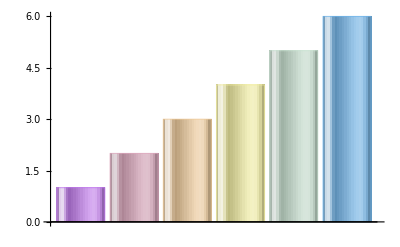

```mathematica
BarChart[Range[6], ChartElementFunction -> "GlassRectangle", 
ChartStyle -> "Pastel"]
```

-Graphics-